```mathematica
Remove["Global`*"];
fd=((2/L)*(1-(d/L)));
fr =((2/H)*(1-(r/H)));
a={d∈Reals,r∈Reals,w∈Reals,H∈Reals,L∈Reals, L>H>w>0,w>r>0, w>d>0};

I1=Simplify[Integrate[Integrate[fd*fr,{d,0,w- r},Assumptions->a],{r,0,w},Assumptions->a],a];

D1=Simplify[Dt[I1,w,Constants -> {L, H}],a];
CDF1 = I1
PDF1 = D1
```

(w^2 (12 H L-4 (H+L) w+w^2))/(6 H^2 L^2)

(2 w (6 H L-3 H w-3 L w+w^2))/(3 H^2 L^2)

```mathematica
b ={d∈Reals,r∈Reals,w∈Reals,H∈Reals,L∈Reals, L>H,w>H>d >0, w>r>0,w>d>0, H> 0, L> 0, L > w};

I2=Apart[Simplify[Integrate[Integrate[fd*fr,{d,H- r,w-r},Assumptions->b],{r,0,H},Assumptions->b]]];
D2=FullSimplify[Dt[I2,w,Constants -> {L, H}],b];

CDF2 = FullSimplify[I2+ Function[w, Evaluate[CDF1]][H],b]
PDF2 = D2
```

-(H^2+4 H (L-w)+6 w (-2 L+w))/(6 L^2)

(2 (H+3 L-3 w))/(3 L^2)

```mathematica
c = {d∈Reals,r∈Reals,w∈Reals,H∈Reals,L∈Reals,w>L>d>H>r>0,H> w-L,H>0, L>0 , w > H, w > L};

I3=Integrate[Integrate[fd*fr,{d, L, w - r},Assumptions->c],{r, 0, w - L},Assumptions->c];
D3=Simplify[Dt[I3,w,Constants -> {L, H}],c];
CDF3 = FullSimplify[I2-I3  +  1 - Function[w, Evaluate[I2 - I3]][H + L],c] 
PDF3 = FullSimplify[D2-D3  , c]
```

-(H^4+4 H^3 (L-w)+4 H (L-w)^3+(L-w)^4+6 H^2 w (-2 L+w))/(6 H^2 L^2)

(2 (H+L-w)^3)/(3 H^2 L^2)

```mathematica
mean = Simplify[Integrate[w * PDF1, {w, 0, H}]  + Integrate[w * PDF2, {w, H, L}] + Integrate[w * PDF3, {w, L, H + L}]] 
CForm[mean]
```

(H+L)/3

(H + L)/3.

```mathematica
TeXForm[mean]
```

\frac{H+L}{3}

```mathematica
variance = Apart[FullSimplify[Integrate[((w - mean)^2 )* PDF1, {w, 0, H}]  + Integrate[((w - mean)^2) * PDF2, {w, H, L}] + Integrate[w((w - mean)^2)* PDF3, {w, L, H + L}]] ]
CForm[variance]
```

(2 H^5+14 H^4 (-1+L)-28 H^3 (-2+L) L+105 L^4+35 H^2 L^2 (-1+4 L))/(1890 L^2)

(2*Power(H,5) + 14*Power(H,4)*(-1 + L) - 28*Power(H,3)*(-2 + L)*L + 105*Power(L,4) + 
     35*Power(H,2)*Power(L,2)*(-1 + 4*L))/(1890.*Power(L,2))

```mathematica
TeXForm[variance]
```

\frac{2 H^5+14 H^4 (L-1)-28 H^3 (L-2) L+35 H^2 L^2 (4 L-1)+105 L^4}{1890 L^2}

```mathematica
CForm[Evaluate[PDF1]]
```

(2*w*(6*H*L - 3*H*w - 3*L*w + Power(w,2)))/(3.*Power(H,2)*Power(L,2))

```mathematica
CForm[Evaluate[PDF2]]
```

(2*(H + 3*L - 3*w))/(3.*Power(L,2))

```mathematica
CForm[Evaluate[PDF3]]
```

(2*Power(H + L - w,3))/(3.*Power(H,2)*Power(L,2))

```mathematica
CForm[Evaluate[CDF1]]
```

(Power(w,2)*(12*H*L - 4*(H + L)*w + Power(w,2)))/(6.*Power(H,2)*Power(L,2))

```mathematica
CForm[Evaluate[CDF2]]
```

-(Power(H,2) + 4*H*(L - w) + 6*w*(-2*L + w))/(6.*Power(L,2))

```mathematica
CForm[Evaluate[CDF3]]
```

-(Power(H,4) + 4*Power(H,3)*(L - w) + 4*H*Power(L - w,3) + Power(L - w,4) + 
      6*Power(H,2)*w*(-2*L + w))/(6.*Power(H,2)*Power(L,2))

```mathematica
TeXForm[Evaluate[CDF1]]
```

\frac{w^2 \left(-4 w (H+L)+12 H L+w^2\right)}{6 H^2 L^2}

```mathematica
TeXForm[Evaluate[CDF2]]
```

-\frac{H^2+4 H (L-w)+6 w (w-2 L)}{6 L^2}

```mathematica
TeXForm[Evaluate[CDF3]]
```

-\frac{H^4+4 H^3 (L-w)+6 H^2 w (w-2 L)+4 H (L-w)^3+(L-w)^4}{6 H^2 L^2}

```mathematica
TeXForm[Evaluate[PDF1]]
```

\frac{2 w \left(6 H L-3 H w-3 L w+w^2\right)}{3 H^2 L^2}

```mathematica
TeXForm[Evaluate[PDF2]]
```

\frac{2 (H+3 L-3 w)}{3 L^2}

```mathematica
TeXForm[Evaluate[PDF3]]
```

\frac{2 (H+L-w)^3}{3 H^2 L^2}

1

2

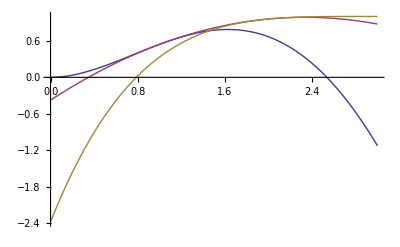

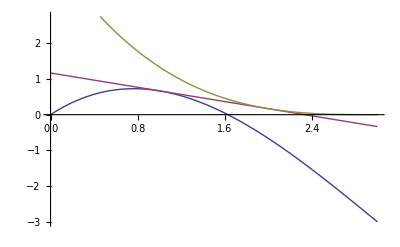

```mathematica
H=1
L=2
Plot[{CDF1,CDF2,CDF3},{w,0,L + H}]
Plot[{PDF1,PDF2,PDF3},{w,0,L+H}]
```

3

4

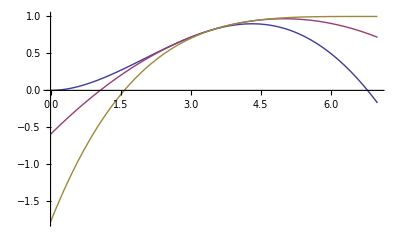

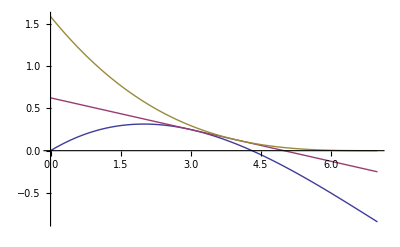

```mathematica
H=3
L=4
Plot[{CDF1,CDF2,CDF3},{w,0,L + H}]
Plot[{PDF1,PDF2,PDF3},{w,0,L  + H}]
```

5

12

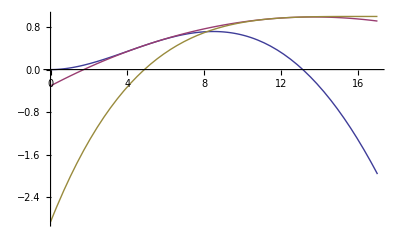

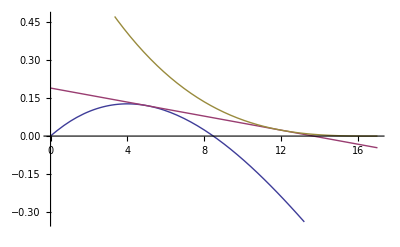

```mathematica
H=5
L=12
Plot[{CDF1,CDF2,CDF3},{w,0,L + H}]
Plot[{PDF1,PDF2,PDF3},{w,0,L + H}]
```